## Flight-gate problem

## Задача № 1

Данные

```mathematica
numberOfFlights = 10;
numberOfGates=3;
maxTime=100;
groundTime:=RandomInteger[{1,10}]
```

```mathematica
arrivalDeparture=
Table[{#,Min[#+groundTime,maxTime]}&@RandomInteger[{0,maxTime}],numberOfFlights]
```

{{39,45},{52,57},{90,100},{42,46},{35,38},{0,1},{77,85},{39,47},{58,63},{84,86}}

```mathematica
gatesCoordinates=RandomInteger[{0,50},{numberOfGates+2,2}];
distanceMatrix=DistanceMatrix[N@gatesCoordinates,DistanceFunction->ManhattanDistance](*1 строка, 1 столбец - это 0 гейт, numberOfGates+2 строка и столбец - гейт m+1, в терминах постановки в классе*);
```

```mathematica
size={numberOfFlights+1,numberOfFlights+1};
flowMatrix=#+#ᵀ&@UpperTriangularize[RandomInteger[{0,100},size]*SparseArray[{i_,i_}->0,size,1]](*1 строка и столбец - гейт 0*);
```

Переменные

```mathematica
xVars=Array[x,{numberOfFlights,numberOfGates+1}];
```

```mathematica
subsetsXVars=Subsets[Flatten[xVars],{2}];
yVars=Cases[subsetsXVars,{_[i_,k_],_[j_,l_]}/;i!=j:>y[i,k,j,l]];
```

```mathematica
vars=Join[Flatten[xVars],yVars];
```

Целевая функция

1) Целевая функция для минимизации рейсов на apron’е

```mathematica
of1=Total[xVars⟦All,-1⟧];
```

2) Целевая функция для минимизации пройденного расстояния пассажирами

```mathematica
Clear[getValueOptimizationFunction2]
getValueOptimizationFunction2[y[i_,k_,j_,l_]]:=If[k!=l,distanceMatrix⟦k+1,l+1⟧*flowMatrix⟦i+1,j+1⟧,0]
```

```mathematica
of2=Total[Map[getValueOptimizationFunction2[#]*#&,yVars]];
```

```mathematica
Clear[getValueOptimizationFunction3]
getValueOptimizationFunction3[x[i_,k_]]:=distanceMatrix⟦1,k+1⟧*flowMatrix⟦1,i+1⟧
```

```mathematica
of3=Total[Map[2*getValueOptimizationFunction3[#]*#&,Flatten[xVars]]];
```

```mathematica
of=10^9 of1+of2+of3;
```

Ограничения

1) Каждый рейс назначен на гейт

```mathematica
con1=Thread[Total[xVars,{2}]==1];
```

2) Запрет наложения рейсов

```mathematica
Clear[getCondition2]
getCondition2[y[i_,k_,j_,l_]]:=(arrivalDeparture⟦i,2⟧-arrivalDeparture⟦j,1⟧)*(arrivalDeparture⟦j,2⟧-arrivalDeparture⟦i,1⟧)
```

```mathematica
con2=Map[
#*getCondition2[#]<=0&,
Cases[yVars,y[i_,k_,j_,l_]/;k==l∧k!=numberOfGates+1]
];
```

3) Бинарность (+ продолжение дальше)

```mathematica
con3=Thread[0<=Flatten[vars]<=1];
```

4-5) Линеаризация y_ikjl

```mathematica
Clear[getCond4]
getCond4[y[i_,k_,j_,l_]]:=xVars⟦i,k⟧+xVars⟦j,l⟧-1;
```

```mathematica
con4=Map[#>=getCond4[#]&,yVars];
```

```mathematica
Clear[getCond5]
getCond5[y[i_,k_,j_,l_]]:={xVars⟦i,k⟧,xVars⟦j,l⟧};
```

```mathematica
con5=Flatten@Map[Thread[{#,#}<=getCond5[#]]&,yVars];
```

```mathematica
dom=#∈Integers&/@vars;
```

Решение

```mathematica
numSol=LinearOptimization[of,Join[con1,con2,con3,con4,con5],dom];
```

```mathematica
solution=Cases[numSol⟦;;Length@Flatten@xVars⟧,(_[i_,k_]->1):>{i,k}]
```

{{1,3},{2,1},{3,1},{4,2},{5,1},{6,1},{7,1},{8,1},{9,1},{10,2}}

```mathematica
arrivalDeparture
```

{{39,45},{52,57},{90,100},{42,46},{35,38},{0,1},{77,85},{39,47},{58,63},{84,86}}

## Задача № 1.1

```mathematica
Clear[getPlotForTuple]
getPlotForTuple[{index_,gate_,arrival_,departure_},colors_,maxDeparture_,numberOfGates_:numberOfGates]:=Plot[gate,{x,arrival,departure},
PlotRange->{{0,maxDeparture},{0,numberOfGates+2}},
PlotLabels->Placed[ToString[index],Below],
PlotStyle->{(gate/.colors),Thickness[0.035]}]
```

```mathematica
Clear[ganttChart]
ganttChart[solution_,arrivalDeparture_,numberOfGates_:numberOfGates,gap_:10]:=Module[
{
solutionExtendedData=Flatten/@Thread[{solution,arrivalDeparture}],
colors=MapIndexed[First[#2]->#1&,RandomColor[numberOfGates+1]],
maxDeparture,
fakePlotY=Range[numberOfGates+1]
},
maxDeparture=Max[solutionExtendedData⟦All,-1⟧]+gap;
Show[
Plot[fakePlotY,{x,0,0.01},
PlotRange->{{0,maxDeparture},{0,numberOfGates+1.5}},
PlotStyle->(fakePlotY/.colors),
PlotLegends->(ToString[#]&/@fakePlotY),
AxesLabel->{"time","gate"},
PlotLabel->Style["Gantt chart",FontFamily->"Times New Roman",FontSize->20]],
Map[getPlotForTuple[#,colors,maxDeparture,numberOfGates]&,solutionExtendedData],
ImageSize->Large
]
]
```

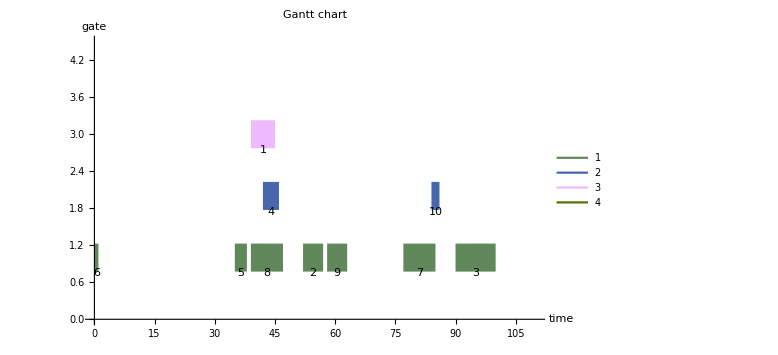

```mathematica
ganttChart[solution,arrivalDeparture]
```

```mathematica
solution
```

{{1,3},{2,1},{3,1},{4,2},{5,1},{6,1},{7,1},{8,1},{9,1},{10,2}}

```mathematica
arrivalDeparture
```

{{39,45},{52,57},{90,100},{42,46},{35,38},{0,1},{77,85},{39,47},{58,63},{84,86}}

## Задача № 2

```mathematica
Clear[greedy]
greedy[arrivalDeparture_,numberOfGates_,arrivalQ_:True,maxQ_:True]:=Module[
{
sortedArrivalDepartureTrueIndex=SortBy[MapIndexed[Join[#1,#2]&,arrivalDeparture],If[arrivalQ,#⟦1⟧&,#⟦2⟧&]],
available=ConstantArray[0,numberOfGates],
result={},
gate,j,
arrival,departure,trueIndex
},
Do[
{arrival,departure,trueIndex}=flightData;
gate=Pick[available,#<arrival&/@available];
If[gate!={},
j=Composition[First,Flatten][Position[available,If[maxQ,Max,Min]@gate]];
available⟦j⟧=departure;
AppendTo[result,{trueIndex,j}],
AppendTo[result,{trueIndex,numberOfGates+1}]
],
{flightData,sortedArrivalDepartureTrueIndex}
];
SortBy[result,First]
]
```

```mathematica
greedySolution=greedy[arrivalDeparture,numberOfGates]
```

{{1,1},{2,2},{3,3},{4,3},{5,1},{6,4},{7,2},{8,2},{9,2},{10,3}}

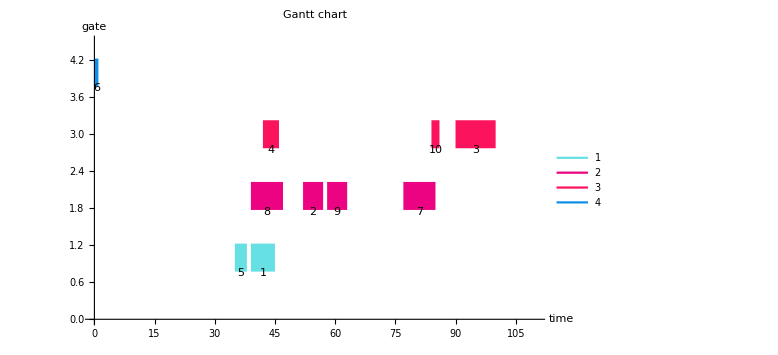

```mathematica
ganttChart[greedySolution,arrivalDeparture]
```